```mathematica
SetDirectory[NotebookDirectory[]];
(* Functions to extract different columns from the tables. *)
extract2[list_]:=Table[{list[[i,1]],list[[i,2]]},{i,Length[list]}]
extract3[list_]:=Table[{list[[i,1]],list[[i,3]]},{i,Length[list]}]
extract4[list_]:=Table[{list[[i,1]],list[[i,4]]},{i,Length[list]}]
extract5[list_]:=Table[{list[[i,1]],list[[i,5]]},{i,Length[list]}]
extract6[list_]:=Table[{list[[i,1]],list[[i,6]]},{i,Length[list]}]
extract7[list_]:=Table[{list[[i,1]],list[[i,7]]},{i,Length[list]}]
extract8[list_]:=Table[{list[[i,1]],list[[i,8]]},{i,Length[list]}]
extract9[list_]:=Table[{list[[i,1]],list[[i,9]]},{i,Length[list]}]
extract10[list_]:=Table[{list[[i,1]],list[[i,10]]},{i,Length[list]}]
extract11[list_]:=Table[{list[[i,1]],list[[i,11]]},{i,Length[list]}]
extract12[list_]:=Table[{list[[i,1]],list[[i,12]]},{i,Length[list]}]
extract13[list_]:=Table[{list[[i,1]],list[[i,13]]},{i,Length[list]}]
extract14[list_]:=Table[{list[[i,1]],list[[i,14]]},{i,Length[list]}]
extract15[list_]:=Table[{list[[i,1]],list[[i,15]]},{i,Length[list]}]
extract16[list_]:=Table[{list[[i,1]],list[[i,16]]},{i,Length[list]}]
extract17[list_]:=Table[{list[[i,1]],list[[i,17]]},{i,Length[list]}]
```

#### Linear Power Spectrum

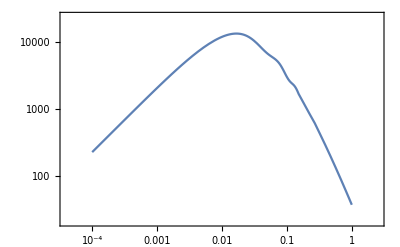

```mathematica
(* This is the linear power spectrum computed by CLASS *)
Plin=Interpolation[Import["output/planck_bestfit_pk.dat"][[5;;]]];
LogLogPlot[Plin[k],{k,0.0001,1},Frame->True]
```

#### Nonlinear Power Spectrum -- Real Space, Non-IR-resummed

```mathematica
(* Import from our code that calculates the nonlinear power spectrum *)
pkreal=Import["output/planck_bestfit_no_IR_pk_nl_pt.dat"][[5;;]];
```

```mathematica
(* Extracting different columns that correspond to different terms in the bias expansion *)
P1loopDM=Interpolation[extract2[pkreal]];
Pctr=Interpolation[extract3[pkreal]];
Id2d2=Interpolation[extract4[pkreal]];
Id2=Interpolation[extract5[pkreal]];
IG2=Interpolation[extract6[pkreal]];
Id2G2=Interpolation[extract7[pkreal]];
IG2G2=Interpolation[extract8[pkreal]];
IFG2=Interpolation[extract9[pkreal]];
Ptree=Interpolation[extract10[pkreal]];
```

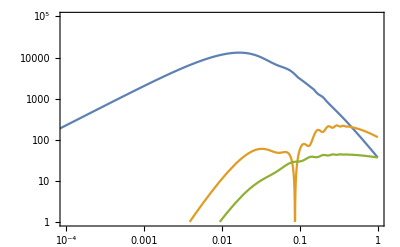

```mathematica
LogLogPlot[{Ptree[k],Abs[P1loopDM[k]],Abs[Pctr[k]]},{k,0.00001,1},PlotRange->{{0.0001,1},{1,100000}},Frame->True]
```

#### Nonlinear Power Spectrum -- Real Space, IR-resummed

```mathematica
(* Import from our code that calculates the nonlinear power spectrum *)
pkrealIR=Import["output/planck_bestfit_pk_nl_pt.dat"][[5;;]];
```

```mathematica
(* Extracting different columns that correspond to different terms in the bias expansion *)
P1loopDMIR=Interpolation[extract2[pkrealIR]];
PctrIR=Interpolation[extract3[pkrealIR]];
Id2d2IR=Interpolation[extract4[pkrealIR]];
Id2IR=Interpolation[extract5[pkrealIR]];
IG2IR=Interpolation[extract6[pkrealIR]];
Id2G2IR=Interpolation[extract7[pkrealIR]];
IG2G2IR=Interpolation[extract8[pkrealIR]];
IFG2IR=Interpolation[extract9[pkrealIR]];
PtreeIR=Interpolation[extract10[pkrealIR]];
```

```mathematica
b1=2;
cs=1;
b2=-1;
bG2=0.1;
bΓ3=-0.1;
cs=0;
R=5;
Pshot=5*10^3;
PggrealIR[k_]:=b1^2 PtreeIR[k]+b1^2 P1loopDMIR[k]+2*b1(R+cs*b1)*PctrIR[k]+b1*b2*Id2IR[k]+b2^2/4*Id2d2IR[k]+2bG2*b1*IG2IR[k]+2b1*(bG2+2/5 bΓ3)*IFG2IR[k]+bG2^2 IG2G2IR[k]+b2*bG2*Id2G2IR[k]+Pshot;
PmmrealIR[k_]:=PtreeIR[k]+P1loopDMIR[k]+2*cs*PctrIR[k];
PgmrealIR[k_]:=b1(PtreeIR[k]+P1loopDMIR[k])+(R+2*cs*b1)*PctrIR[k]+b2/2*Id2IR[k]+bG2*IG2IR[k];
```

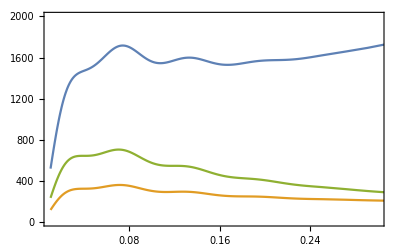

```mathematica
Plot[{k*PggrealIR[k],k*PmmrealIR[k],k*PgmrealIR[k]},{k,0.01,1},PlotRange->{{0.01,0.3},{1,2000}},Frame->True]
```

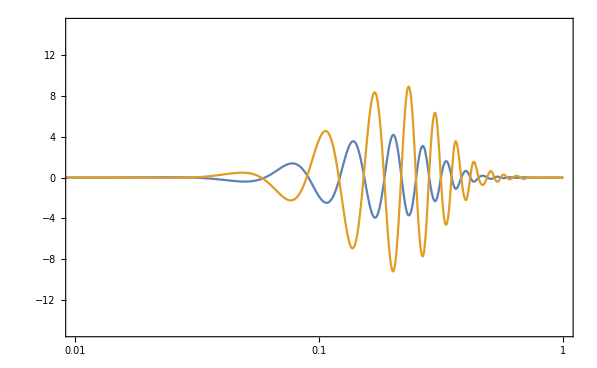

```mathematica
(* No broadband difference. *)
LogLinearPlot[{Ptree[k]-PtreeIR[k],P1loopDM[k]-P1loopDMIR[k]},{k,0.0001,1},PlotRange->{{0.01,1},{-15,15}},Frame->True]
```

#### Nonlinear Power Spectrum -- Redshift Space, IR-resummed

```mathematica
(* In case you are interested in non-IR-resummed multipoles, just load another file, like for the real space above. *)
```

```mathematica
P0data=Import["output/planck_bestfit_pk_rsd_0.dat"][[5;;]];
Pvv0=Interpolation[extract2[P0data]];
Pvd0=Interpolation[extract3[P0data]];
Pdd0=Interpolation[extract4[P0data]];
Pctr0=Interpolation[extract5[P0data]];
P0d2d2=Interpolation[extract6[P0data]];
P0b1b2=Interpolation[extract7[P0data]];
P0b2=Interpolation[extract8[P0data]];
P0b1bG2=Interpolation[extract9[P0data]];
P0bG2=Interpolation[extract10[P0data]];
P0d2bG2=Interpolation[extract11[P0data]];
P0bG2bG2=Interpolation[extract12[P0data]];
P0FG2b1=Interpolation[extract13[P0data]];
P0FG2=Interpolation[extract14[P0data]];
P0vvtree=Interpolation[extract15[P0data]];
P0vdtree=Interpolation[extract16[P0data]];
P0ddtree=Interpolation[extract17[P0data]];

Pdata2=Import["output/planck_bestfit_pk_rsd_2.dat"][[5;;]];
Pvv2=Interpolation[extract2[Pdata2]];
Pvd2=Interpolation[extract3[Pdata2]];
Pdd2=Interpolation[extract4[Pdata2]];
Pctr2=Interpolation[extract5[Pdata2]];
P2b1b2=Interpolation[extract6[Pdata2]];
P2b2=Interpolation[extract7[Pdata2]];
P2b1bG2=Interpolation[extract8[Pdata2]];
P2bG2=Interpolation[extract9[Pdata2]];
P2FG2=Interpolation[extract10[Pdata2]];
P2vvtree=Interpolation[extract14[Pdata2]];
P2vdtree=Interpolation[extract15[Pdata2]];

Pdata4=Import["output/planck_bestfit_pk_rsd_4.dat"][[5;;]];
Pvv4=Interpolation[extract2[Pdata4]];
Pvd4=Interpolation[extract3[Pdata4]];
Pdd4=Interpolation[extract4[Pdata4]];
Pctr4=Interpolation[extract5[Pdata4]];
P4b2=Interpolation[extract6[Pdata4]];
P4bG2=Interpolation[extract7[Pdata4]];
P4b1b2=Interpolation[extract8[Pdata4]];
P4b1bG2=Interpolation[extract9[Pdata4]];
P4b2b2=Interpolation[extract10[Pdata4]];
P4b2bG2=Interpolation[extract11[Pdata4]];
P4bG2bG2=Interpolation[extract12[Pdata4]];
P4vvtree=Interpolation[extract13[Pdata4]];
```

```mathematica
cs0=5;
cs2=15;
cs4=-5;
b4=100;
f=0.793447;
```

```mathematica
(* The linear part *)
Pgg0tree[k_]:=P0vvtree[k]+b1*P0vdtree[k]+b1^2 P0ddtree[k];
Pgg2tree[k_]:=P2vvtree[k]+b1*P2vdtree[k];
Pgg4tree[k_]:=P4vvtree[k];
```

```mathematica
(* The one-loop part *)
Pgg0loop[k_]:=Pvv0[k]+b1*Pvd0[k]+b1^2 Pdd0[k]+2cs0*b1^2*Pctr0[k]+b1*b2*P0b1b2[k]+b2^2/4*P0d2d2[k]+bG2*b1*P0b1bG2[k]+2b1*(bG2+0.4*bΓ3)*P0FG2b1[k]+2(bG2+0.4*bΓ3)*P0FG2[k]+bG2^2 P0bG2bG2[k]+b2*bG2*P0d2bG2[k]+bG2*P0bG2[k]+b2*P0b2[k]+Pshot+ f^2*b4*k^2*(f^2/9+2*f*b1/7+b1^2/5)*(35/8)*Pctr4[k];
Pgg2loop[k_]:=Pvv2[k]+b1*Pvd2[k]+b1^2 Pdd2[k]+2*b1*cs2*Pctr2[k]+b1*b2*P2b1b2[k]+bG2*b1*P2b1bG2[k]+2(bG2+0.4*bΓ3)*P2FG2[k]+bG2*P2bG2[k]+b2*P2b2[k] + f^2*b4*k^2*(f^2*70+165*f*b1+b1^2*99)*(4/693)*(35/8)*Pctr4[k];

Pgg4loop[k_]:=Pvv4[k]+b1*Pvd4[k]+b1^2 Pdd4[k]+2cs4*Pctr4[k]+b1*b2*P4b1b2[k]+bG2*b1*P4b1bG2[k]+b2*P4b2[k]+bG2*P4bG2[k]+bG2*P2bG2[k]+b2*P2b2[k] +b2^2/4*P4b2b2[k]+bG2*b2*P4b2bG2[k]+bG2^2 P4bG2bG2[k]+ f^2*b4*k^2*(f^2*210+390*f*b1+b1^2*143)*(8/5005)*(35/8)*Pctr4[k];
```

```mathematica
(* The total power spectra multipoles *)
Pfull0[k_]:=Pgg0loop[k]+Pgg0tree[k];
Pfull2[k_]:=Pgg2loop[k]+Pgg2tree[k];
Pfull4[k_]:=Pgg4loop[k]+Pgg4tree[k];
```

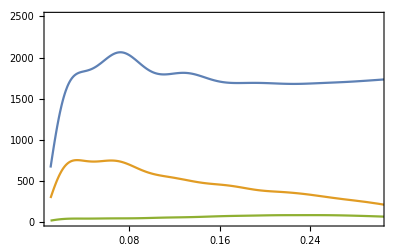

```mathematica
Plot[{k*Pfull0[k],k*Pfull2[k],k*Pfull4[k]},{k,0.01,0.5},PlotRange->{{0.01,0.3},{1,2500}},Frame->True]
```

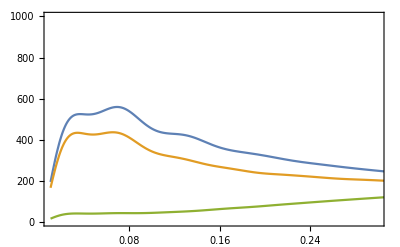

```mathematica
(* The matter-matter part *)
Pmm0[k_]:=P0vvtree[k]+P0vdtree[k]+P0ddtree[k]+Pvv0[k]+Pvd0[k]+Pdd0[k]+2cs0*Pctr0[k];
Pmm2[k_]:=P2vvtree[k]+P2vdtree[k]+Pvv2[k]+Pvd2[k]+Pdd2[k]+2cs2*Pctr2[k];
Pmm4[k_]:=P4vvtree[k]+Pvv4[k]+Pvd4[k]+Pdd4[k]+2cs4*Pctr4[k];
Plot[{k*Pmm0[k],k*Pmm2[k],k*Pmm4[k]},{k,0.01,0.4},PlotRange->{{0.01,0.3},{1,1000}},Frame->True]
```

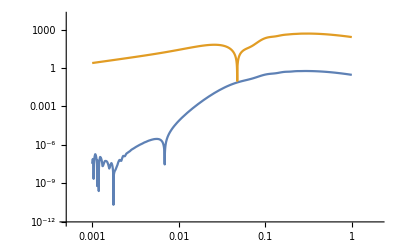

```mathematica
(* This is the comparison of the hexadecapole contribution that has been generated by the leakage of the monopole and quadrupole through AP and IR resummation - it is absolutely neglegible. This is why we droppem them from classy *)
LogLogPlot[{Abs[b1*b2*P4b1b2[k]+bG2*b1*P4b1bG2[k]+b2^2/4*P4b2b2[k]+bG2*b2*P4b2bG2[k]+bG2^2 P4bG2bG2[k]],Abs[b1*Pvd4[k]+b1^2 Pdd4[k]+2cs4*Pctr4[k]+b1*b2*P4b1b2[k]+bG2*b1*P4b1bG2[k]+b2*P4b2[k]+bG2*P4bG2[k]+bG2*P2bG2[k]+b2*P2b2[k] +b2^2/4*P4b2b2[k]+bG2*b2*P4b2bG2[k]+bG2^2 P4bG2bG2[k]]},{k,0.001,1}]
```

```mathematica
(*Finally, we present the function that converts our Fourier-space power spectra into the position space correlation functions*)
```

```mathematica
Pnoir[k_]:=Ptree[k]+P1loopDM[k];
Pir[k_]:=PtreeIR[k]+P1loopDMIR[k];
```

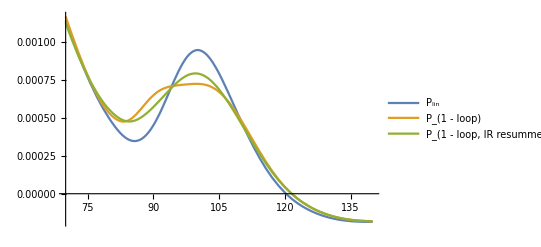

```mathematica
kBins[Nmax0_,k00_,kmax0_]:=Module[{Nmax=Nmax0,k0=k00,kmax=kmax0,Δ,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
result=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
result
];
CoeffPow0noir[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Pnoir[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[cnsym]}];
result
];
CoeffPow0ir[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Pir[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[cnsym]}];
result
];
CoeffPowlin[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[cnsym]}];
result
];
bias=-0.0001//N;
Nmax=240;
k0=10^-5;
kmax=10;

rlist2=Join[Table[x,{x,1,1.9,0.1}],Table[x,{x,1.91,2.14,0.01}],Table[x,{x,2.15,2.35,0.05}]];

J0[r_,ν_]:=-1/2 ⅈ ((-ⅈ r)^ν-(ⅈ r)^ν) r^(-3-2 ν) Gamma[2+ν]/(2 Pi^2);

cn0=CoeffPow0noir[bias,Nmax,k0,kmax];
t0=Table[{10^x,Sum[Re[cn0⟦j,1⟧J0[10^x,cn0⟦j,2⟧]],{j,Length[cn0]}]},{x,rlist2}];
xi0=Interpolation[t0];

cn0lin=CoeffPowlin[bias,Nmax,k0,kmax];
t0lin=Table[{10^x,Sum[Re[cn0lin⟦j,1⟧J0[10^x,cn0lin⟦j,2⟧]],{j,Length[cn0lin]}]},{x,rlist2}];
xi0lin=Interpolation[t0lin];

cn0ir=CoeffPow0ir[bias,Nmax,k0,kmax];
t0ir=Table[{10^x,Sum[Re[cn0ir⟦j,1⟧J0[10^x,cn0ir⟦j,2⟧]],{j,Length[cn0ir]}]},{x,rlist2}];
xi0ir=Interpolation[t0ir];

Plot[{xi0lin[r],xi0[r],xi0ir[r]},{r,70,140},PlotLegends->Placed[LineLegend[{"P_lin","P_(1 - loop)","P_(1 - loop,  IR resummed)"}],{0.8,0.8}]]
```

```mathematica
(*These are the master functions if one wants to compute the qiadrupole and hexadecapole correlation functions. Just replace J0 to J2 or J4 *)
```

```mathematica
J2[r_,ν_]:=(r^(-3-ν) (3+ν) Gamma[2+ν] Sin[(π ν)/2])/ν/(2 Pi^2);
J4[r_,ν_]:=(2^(1+ν) √π r^(-3-ν) Gamma[1/2 (3+4+ν)])/Gamma[(4-ν)/2]/(2 Pi^2);
```

```mathematica
(*the loop corrections need to be regularized at high k. We apply the exponetial cutoff for high k's for this reason*)
```

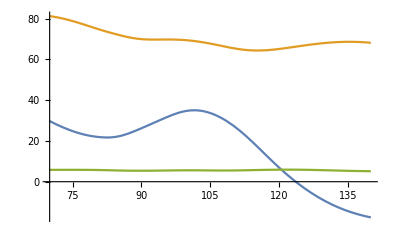

```mathematica
Pgg0[k_]:=P0vvtree[k]+b1*P0vdtree[k]+b1^2 P0ddtree[k]+Pvv0[k]+b1*Pvd0[k]+b1^2 Pdd0[k]+b1*b2*P0b1b2[k]+Pshot+(2*cs0*b1^2*Pctr0[k]+f^2*b4*k^2*(f^2/9+2*f*b1/7+b1^2/5)*(35/8)*Pctr4[k]+b2^2/4*P0d2d2[k]+bG2*b1*P0b1bG2[k]+2b1*(bG2+0.4*bΓ3)*P0FG2b1[k]+2(bG2+0.4*bΓ3)*P0FG2[k]+bG2^2 P0bG2bG2[k]+b2*bG2*P0d2bG2[k]+bG2*P0bG2[k]+b2*P0b2[k])*Exp[-k^4] ;

Pgg4loop[k_]:=Pvv4[k]+b1*Pvd4[k]+b1^2 Pdd4[k]+2cs4*Pctr4[k]+b1*b2*P4b1b2[k]+bG2*b1*P4b1bG2[k]+b2*P4b2[k]+bG2*P4bG2[k]+bG2*P2bG2[k]+b2*P2b2[k] +b2^2/4*P4b2b2[k]+bG2*b2*P4b2bG2[k]+bG2^2 P4bG2bG2[k]+ f^2*b4*k^2*(f^2*210+390*f*b1+b1^2*143)*(8/5005)*(35/8)*Pctr4[k];
CoeffPow0[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Pgg0[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[cnsym]}];
result
];

CoeffPow2[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Pfull2[kn⟦i⟧]Exp[-(kn⟦i⟧)^4]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[cnsym]}];
result
];
CoeffPow4[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Pfull4[kn⟦i⟧]Exp[-(kn⟦i⟧)^2]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[cnsym]}];
result
];
ClearAll[cn0,t0,xi0]
cn0=CoeffPow0[bias,Nmax,k0,kmax];
t0=Table[{10^x,Sum[Re[cn0⟦j,1⟧J0[10^x,cn0⟦j,2⟧]],{j,Length[cn0]}]},{x,rlist2}];
xi0=Interpolation[t0];

cn2=CoeffPow2[bias,Nmax,k0,kmax];
t2=Table[{10^x,Sum[Re[cn2⟦j,1⟧J2[10^x,cn2⟦j,2⟧]],{j,Length[cn2]}]},{x,rlist2}];
xi2=Interpolation[t2];

cn4=CoeffPow4[bias,Nmax,k0,kmax];
t4=Table[{10^x,Sum[Re[cn4⟦j,1⟧J4[10^x,cn4⟦j,2⟧]],{j,Length[cn4]}]},{x,rlist2}];
xi4=Interpolation[t4];

Plot[{r^2*xi0[r],r^2*xi2[r],r^2*xi4[r]},{r,70,140}]
```